```mathematica
uExact[x_,t_]:=1/2(E^(2 π^(3/2)t)Sin[2π x-2 π^(3/2)t]+E^(-2 π^(3/2)t)Sin[2π x+2 π^(3/2)t]);
vExact[x_,t_]:=ⅇ^(-2 π^(3/2) t) π^(3/2) (Cos[2 π (√π t+x)]-Sin[2 π (√π t+x)]-ⅇ^(4 π^(3/2) t) (Cos[2 π^(3/2) t-2 π x]+Sin[2 π^(3/2) t-2 π x]));
```

```mathematica
n=10;
m=100;
dx=1/m;
dt=0.3/n;
```

```mathematica
plotList[w_]:=ListPlot[{Table[x,{x,0,1-Exp[-10],1/(Length[w])}],w}//Transpose];
```

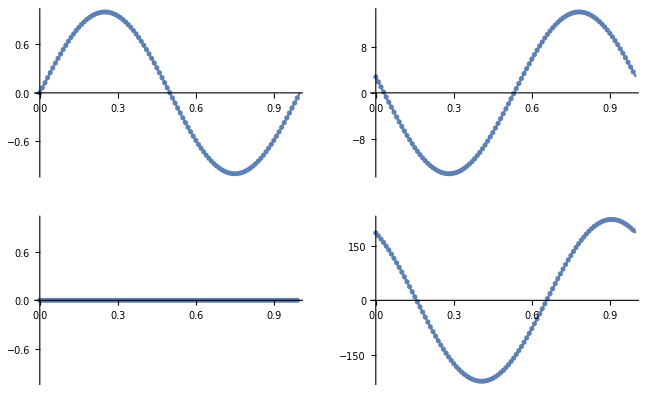

```mathematica
u=Import["/home/abe/uu/numpde/numPDE/F4a/u.dat","Table"];
v=Import["/home/abe/uu/numpde/numPDE/F4a/v.dat","Table"];
GraphicsGrid[{{Show[plotList[u[[1]]],Plot[uExact[x,0],{x,0,1}]],Show[plotList[u[[-1]]],Plot[uExact[x,0.3],{x,0,1}]]},{Show[plotList[v[[1]]],Plot[vExact[x,0],{x,0,1}]],Show[plotList[v[[-1]]],Plot[vExact[x,0.3],{x,0,1}]]}}]
```

```mathematica
uCompared=Show[ListPointPlot3D[u,PlotStyle->{PointSize[Large]}],
Plot3D[uExact[(xip-1)*dx,(tip-1)*dt],{xip,1,m},{tip,1,n+1}],AxesLabel->{"i+1","n+1","u"},PlotLabel->"u compared with exact solution"];
vCompared=Show[ListPointPlot3D[v,PlotStyle->{PointSize[Large]}],
Plot3D[vExact[(xip-1)*dx,(tip-1)*dt],{xip,1,m},{tip,1,n+1}],AxesLabel->{"i+1","n+1","v"},PlotLabel->"v compared with exact solution"];
uError=ListPointPlot3D[u-(Table[uExact[(xip-1)*dx,(tip-1)*dt],{xip,1,m},{tip,1,n+1}]//Transpose),AxesLabel->{"i+1","n+1","u"},PlotLabel->"Absolute error in u"];
vError=ListPointPlot3D[v-(Table[vExact[(xip-1)*dx,(tip-1)*dt],{xip,1,m},{tip,1,n+1}]//Transpose),AxesLabel->{"i+1","n+1","v"},PlotLabel->"Absolute error in v"];
uErrorRelative=ListPointPlot3D[(Table[(u[[tip,xip]]-#)/(#+10^-10)&@uExact[(xip-1)*dx,(tip-1)*dt],{xip,1,m},{tip,1,n+1}]//Transpose),AxesLabel->{"i+1","n+1","v"},PlotLabel->"Relative error in u"];
vErrorRelative=ListPointPlot3D[(Table[(v[[tip,xip]]-#)/(#+10^-10)&@vExact[(xip-1)*dx,(tip-1)*dt],{xip,1,m},{tip,1,n+1}]//Transpose),AxesLabel->{"i+1","n+1","v"},PlotLabel->"Relative error in v"];
GraphicsGrid[{{uCompared,vCompared},{uError,vError},{uErrorRelative,vErrorRelative}},ImageSize->800];
```

```mathematica
Export["uCompared.png",uCompared]
```

uCompared.png

```mathematica
Manipulate[GraphicsRow[{
Show[Plot[uExact[x,t],{x,0,1},PlotRange->{{0,1},{-10,10}}],plotList[u[[Ceiling[0.01+Length[u]*(t/0.3)]]]]],
Show[Plot[vExact[x,t],{x,0,1},PlotRange->{{0,1},{-200,200}}],plotList[v[[Ceiling[0.01+Length[v]*(t/0.3)]]]]]},ImageSize->Large],{t,0,0.3,0.3/n}]
```